# Haldane模型计算笔记

- 写出了哈密顿量
- 计算了k，k’处泰勒展开
- 计算了陈数并画图

## 1.写出哈密顿量

```mathematica
(*1.分质量项、最近邻项、次近邻项写出哈密顿量*)
h12=t1*E^(I*k.a1)+t1*E^(I*k.a2)+t1*E^(I*k.a3);
h21=t1*E^(-I*k.a1)+t1*E^(-I*k.a2)+t1*E^(-I*k.a3);
h211=t2*E^(I*ϕ)*E^(I*k.b1)+t2*E^(I*ϕ)*E^(I*k.b2)+t2*E^(I*ϕ)*E^(I*k.b3)+t2*E^(-I*ϕ)*E^(-I*k.b1)+t2*E^(-I*ϕ)*E^(-I*k.b2)+t2*E^(-I*ϕ)*E^(-I*k.b3);
h222=t2*E^(-I*ϕ)*E^(I*k.b1)+t2*E^(-I*ϕ)*E^(I*k.b2)+t2*E^(-I*ϕ)*E^(I*k.b3)+t2*E^(I*ϕ)*E^(-I*k.b1)+t2*E^(I*ϕ)*E^(-I*k.b2)+t2*E^(I*ϕ)*E^(-I*k.b3);
H0={{M,0},{0,-M}};
H1={{0,h12},{h21,0}};
H2={{h211,0},{0,h222}};
H=H0+H1+H2//ExpToTrig//Expand;
```

## 2.定义数值和向量

```mathematica
(*2.定义a,a1,b1等数值，有用，未注释；
计算点乘的数值没有用处，已注释*)
a=1;
a1={0,a};a2={-(√3)/2 a,-a/2};a3={(√3)/2 a,-a/2};
b1=a2-a3;
b2=a3-a1;
b3=a1-a2;
(*K={(4π)/(3 √3),0};K1={-(4π)/(3 √3),0}*)
(*Ω=Cross[a1,a2].a3;*)
(*b1=(2*π*Cross[a2,a3])/Ω*)
(*{K.a1,K.a2,K.a3}
{K.b1,K.b2,K.b3}
{K1.a1,K1.a2,K1.a3}
{K1.b1,K1.b2,K1.b3}*)
```

## 3.写出表达式并计算展开

```mathematica
(*3.1  k取数值时可以算出四个参量具体数值*)
(*k={4 π/(3 √3),0}，k1={4 π/(3 √3),0}*)
(*3.2  k保留{kx，ky}形式适用于计算级数展开*)
k={kx,ky};
ϵ=2t2Cos[ϕ](Cos[k.b1]+Cos[k.b2]+Cos[k.b3]);
dx=t1(Cos[k.a1]+Cos[k.a2]+Cos[k.a3]);
dy=t1(Sin[k.a1]+Sin[k.a2]+Sin[k.a3]);
dz=M-2t2*Sin[ϕ](Sin[k.b1]+Sin[k.b2]+Sin[k.b3]);(*注意t2和Sin不要写到一起了，不然会认为是一个变量*)
d={dx,dy,dz};(*在这里一并把d定义了，也确实应该这样写，其应用在第四节中*)
ϵ;
dx;
dy;
dz;
```

```mathematica
(*在k={(4π)/(3 √3)，0}处泰勒展开*)
"k处展开结果："
Series[ϵ/.{kx-> (4π)/(3 √3)+δkx}/.{ky-> 0+δky},{δkx,0,1},{δky,0,1}]
Series[dx/.{kx-> (4π)/(3 √3)+δkx}/.{ky-> 0+δky},{δkx,0,1},{δky,0,1}]
Series[dy/.{kx-> (4π)/(3 √3)+δkx}/.{ky-> 0+δky},{δkx,0,1},{δky,0,1}]
Series[dz/.{kx-> (4π)/(3 √3)+δkx}/.{ky-> 0+δky},{δkx,0,1},{δky,0,1}]
```

k处展开结果：

(-3 t2Cos[ϕ]+O[δky]^2)+O[δky]^2 δkx+O[δkx]^2

O[δky]^2+(-(3 t1)/2+O[δky]^2) δkx+O[δkx]^2

((3 t1 δky)/2+O[δky]^2)+((3 t1 δky)/4+O[δky]^2) δkx+O[δkx]^2

((M-3 √3 t2 Sin[ϕ])+O[δky]^2)+O[δky]^2 δkx+O[δkx]^2

```mathematica
(*在k={-(4π)/(3 √3)，0}处泰勒展开*)
"k'处展开结果："
Series[ϵ/.{kx-> (4π)/(3 √3)+δkx}/.{ky-> 0+δky},{δkx,0,1},{δky,0,1}]
Series[dx/.{kx-> -(4π)/(3 √3)+δkx}/.{ky-> 0+δky},{δkx,0,1},{δky,0,1}]
Series[dy/.{kx-> -(4π)/(3 √3)+δkx}/.{ky-> 0+δky},{δkx,0,1},{δky,0,1}]
Series[dz/.{kx-> -(4π)/(3 √3)+δkx}/.{ky-> 0+δky},{δkx,0,1},{δky,0,1}]
```

k'处展开结果：

(-3 t2Cos[ϕ]+O[δky]^2)+O[δky]^2 δkx+O[δkx]^2

O[δky]^2+((3 t1)/2+O[δky]^2) δkx+O[δkx]^2

((3 t1 δky)/2+O[δky]^2)+(-(3 t1 δky)/4+O[δky]^2) δkx+O[δkx]^2

((M+3 √3 t2 Sin[ϕ])+O[δky]^2)+O[δky]^2 δkx+O[δkx]^2

## 4.计算陈数

```mathematica
(*4.1 定义陈数积分表达式*)
temp=-1/(4π)*Cross[D[d,kx],D[d,ky]].d/Norm[d]^3;
f[M0_,t10_,t20_,ϕ0_,kx0_,ky0_]:=temp/.{M-> M0,t1-> t10,t2-> t20,ϕ-> ϕ0,kx-> kx0,ky-> ky0}
f[1,4,1,-π/2,1,1]//N;(*=0.0271184,测试用*)
NIntegrate[f[1,4,1,π/2,kx0,ky0],{kx0,-(4 √3 π)/9,(2 √3 π)/9},{ky0,-(2π)/3,(2π)/3}]
```

-1.

```mathematica
(*定义计算范围*)
nϕ=100;(*ϕ的撒点个数*)
ϕ0=Array[#&,nϕ,{-π,π}]//N;(*ϕ的撒点范围*)
nM=100;(*M/t2的撒点个数*)
M0=Array[#&,nM,{-3 √3,3 √3}]//N;(*M/t2的撒点范围*)
```

```mathematica
(*计算陈数*)(*会出现很多报错，不用理会*)
ncdata=ParallelTable[{ϕ0[[i]],M0[[j]],NIntegrate[f[M0[[j]],4,1,ϕ0[[i]],kx0,ky0],{kx0,-(4 √3 π)/9,(2 √3 π)/9},{ky0,-(2π)/3,(2π)/3},AccuracyGoal->5]},{i,1,nϕ},{j,1,nM}];
```

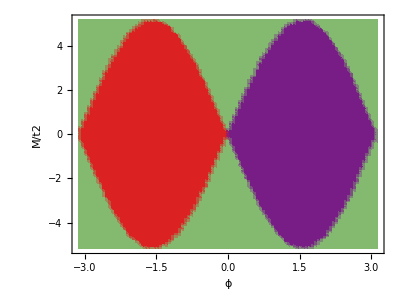

```mathematica
(*整理数据并画图*)
ncdatanew=Flatten[ncdata,1];
ListDensityPlot[ncdatanew,PlotLegends->Automatic,FrameLabel->{"ϕ","M/t2"},ColorFunction->"Rainbow",AspectRatio->3/4]
```